```mathematica
SetDirectory["G:\\johnny\\matlab\\jlhbpe\\2016_10_projects"]
```

G:\johnny\matlab\jlhbpe\2016_10_projects

```mathematica
SetDirectory["~/g/johnny/matlab/jlhbpe/2016_10_projects"]
```

/media/jotelha/storage/windows/Users/jotelha/Google Docs/johnny/matlab/jlhbpe/2016_10_projects

## Import data

```mathematica
adMass1mA=Import["zhang2015control_adsorption_mass_fig4_0_1mA.txt","Table"][[3;;]];
```

```mathematica
adMass2mA=Import["zhang2015control_adsorption_mass_fig4_0_2mA.txt","Table"][[3;;]];
```

```mathematica
adMass4mA=Import["zhang2015control_adsorption_mass_fig4_0_4mA.txt","Table"][[3;;]];
```

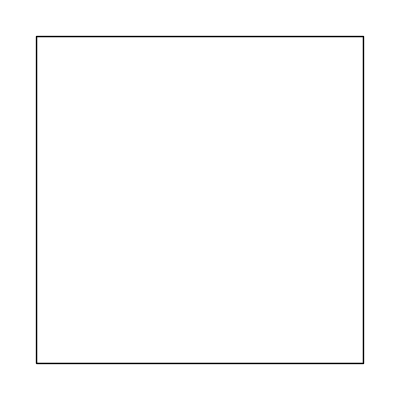

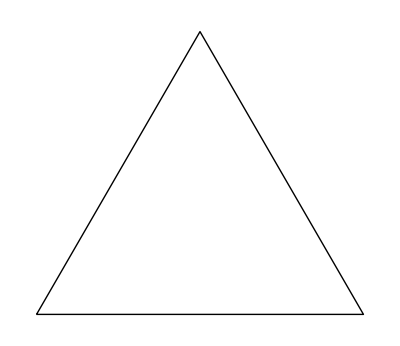

```mathematica
{m1,m2,m3}=Graphics/@{Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}],Circle[{0,0},1],Line[{{-0.5,-0.5},{0.5,-0.5},{0,(Sqrt[3]-1)/2},{-0.5,-0.5}}]}
```

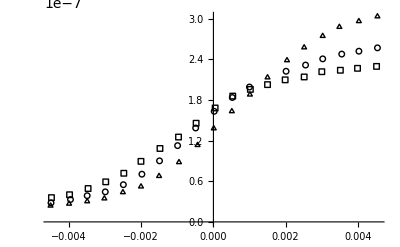

```mathematica
trueMassPlot=ListPlot[{adMass1mA,adMass2mA,adMass4mA},PlotStyle->Black,PlotMarkers->{{□,Medium},{○,Medium},{△,Medium}}]
```

```mathematica
plegend=PointLegend[Table[Black,{3}],{"1 mA","2 mA","4 mA"},LegendMarkerSize->{10,10},LegendMarkers->{{m1,1},{m2,1},{m3,1}},LabelStyle->{GrayLevel[0.0],12}]
```

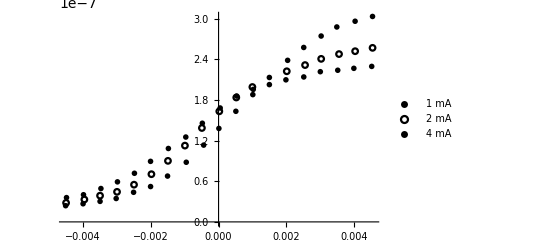

```mathematica
trueMassPlotWithLegend=ListPlot[{adMass1mA,adMass2mA,adMass4mA},PlotStyle->Black,PlotMarkers->Table[{s,0.03},{s,{m1,m2,m3}}],PlotLegends->Placed[plegend,{0.15,0.75}]]
```

```mathematica
dat1mA=Import["zhang2015control_surface_data_0_1mA.txt","Data"][[2;;]];
```

```mathematica
dat2mA=Import["zhang2015control_surface_data_0_2mA.txt","Data"][[2;;]];
```

```mathematica
dat4mA=Import["zhang2015control_surface_data_0_4mA.txt","Data"][[2;;]];
```

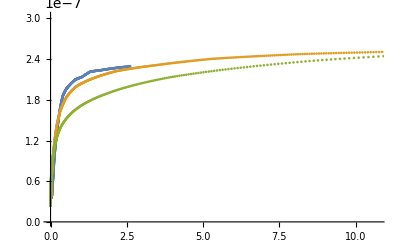

```mathematica
refPlot=ListPlot[{Table[{dat1mA[[n]][[2]],dat1mA[[n]][[3]]},{n,1,Length[dat1mA]}],
Table[{dat2mA[[n]][[2]],dat2mA[[n]][[3]]},{n,1,Length[dat2mA]}],
Table[{dat4mA[[n]][[2]],dat4mA[[n]][[3]]},{n,1,Length[dat4mA]}]}]
```

```mathematica
refIsotherm1mA=Table[{dat1mA[[n]][[2]],dat1mA[[n]][[3]]},{n,1,Length[dat1mA]}];
```

```mathematica
refIsotherm2mA=Table[{dat2mA[[n]][[2]],dat2mA[[n]][[3]]},{n,1,Length[dat2mA]}];
```

```mathematica
refIsotherm4mA=Table[{dat4mA[[n]][[2]],dat4mA[[n]][[3]]},{n,1,Length[dat4mA]}];
```

```mathematica
refReverseIsotherm1mA=Table[{dat1mA[[n]][[3]],dat1mA[[n]][[2]]},{n,1,Length[dat1mA]}];
```

```mathematica
refReverseIsotherm2mA=Table[{dat2mA[[n]][[3]],dat2mA[[n]][[2]]},{n,1,Length[dat2mA]}];
```

```mathematica
refReverseIsotherm4mA=Table[{dat4mA[[n]][[3]],dat4mA[[n]][[2]]},{n,1,Length[dat4mA]}];
```

```mathematica
refReverseLogIsotherm1mA=Table[{dat1mA[[n]][[3]],Log[dat1mA[[n]][[2]]]},{n,1,Length[dat1mA]}];
```

```mathematica
refReverseLogIsotherm2mA=Table[{dat2mA[[n]][[3]],Log[dat2mA[[n]][[2]]]},{n,1,Length[dat2mA]}];
```

```mathematica
refReverseLogIsotherm4mA=Table[{dat4mA[[n]][[3]],Log[dat4mA[[n]][[2]]]},{n,1,Length[dat4mA]}];
```

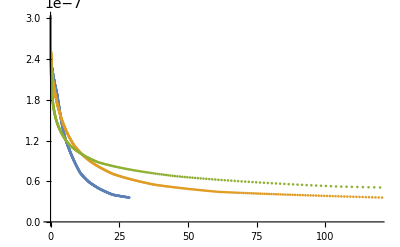

```mathematica
ListPlot[{Table[{1/dat1mA[[n]][[2]],dat1mA[[n]][[3]]},{n,1,Length[dat1mA]}],
Table[{1/dat2mA[[n]][[2]],dat2mA[[n]][[3]]},{n,1,Length[dat2mA]}],
Table[{1/dat4mA[[n]][[2]],dat4mA[[n]][[3]]},{n,1,Length[dat4mA]}]}]
```

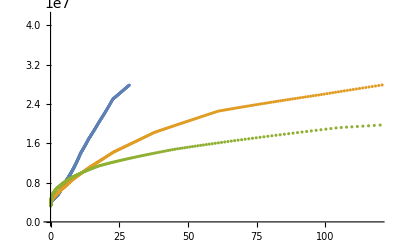

```mathematica
ListPlot[{Table[{1/dat1mA[[n]][[2]],1/dat1mA[[n]][[3]]},{n,1,Length[dat1mA]}],
Table[{1/dat2mA[[n]][[2]],1/dat2mA[[n]][[3]]},{n,1,Length[dat2mA]}],
Table[{1/dat4mA[[n]][[2]],1/dat4mA[[n]][[3]]},{n,1,Length[dat4mA]}]}]
```

## Reference Plots :

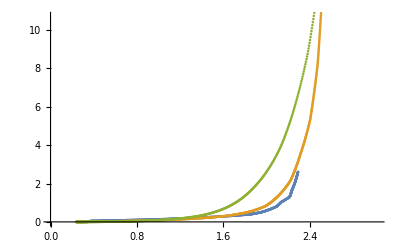

```mathematica
refReverseIsothermPlot=ListPlot[{refReverseIsotherm1mA,refReverseIsotherm2mA,refReverseIsotherm4mA}]
```

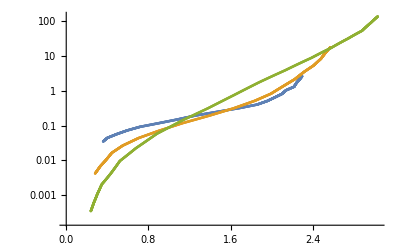

```mathematica
refReverseIsothermLogPlot=ListLogPlot[{refReverseIsotherm1mA,refReverseIsotherm2mA,refReverseIsotherm4mA}]
```

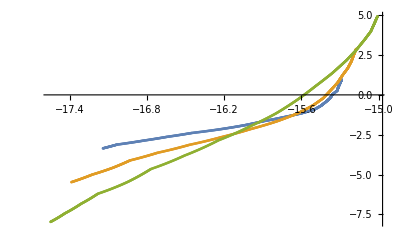

```mathematica
refReverseIsothermLogLogPlot=ListPlot[Log[{refReverseIsotherm1mA,refReverseIsotherm2mA,refReverseIsotherm4mA}]]
```

## Frumkin and Bockris Log fits

```mathematica
First[refReverseLogIsotherm4mA][[1]]
```

2.39057×10^-8

```mathematica
First[refReverseLogIsotherm2mA][[1]]
```

2.81088×10^-8

```mathematica
First[refReverseLogIsotherm1mA][[1]]
```

3.59078×10^-8

```mathematica
Last[refReverseLogIsotherm4mA][[1]]
```

3.02975×10^-7

```mathematica
Last[refReverseLogIsotherm2mA][[1]]
```

2.56801×10^-7

```mathematica
Last[refReverseLogIsotherm1mA][[1]]
```

2.29391×10^-7

```mathematica
refReverseLogIsotherm4mANormCorrected = Table[{(refReverseLogIsotherm4mA[[n,1]]-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]]),refReverseLogIsotherm4mA[[n,2]]},{n,1,Length[refReverseLogIsotherm4mA]}];
```

```mathematica
refReverseLogIsotherm2mANormCorrected = Table[{(refReverseLogIsotherm2mA[[n,1]]-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]]),refReverseLogIsotherm2mA[[n,2]]},{n,1,Length[refReverseLogIsotherm2mA]}];
```

```mathematica
refReverseLogIsotherm1mANormCorrected = Table[{(refReverseLogIsotherm4mA[[n,1]]-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]]),refReverseLogIsotherm1mA[[n,2]]},{n,1,Length[refReverseLogIsotherm1mA]}];
```

```mathematica
linearizedReverseIsotherm4mA=Table[{refReverseLogIsotherm4mANormCorrected[[n,1]],refReverseLogIsotherm4mANormCorrected[[n,2]]-Log[refReverseLogIsotherm4mANormCorrected[[n,1]]]+Log[1-refReverseLogIsotherm4mANormCorrected[[n,1]]]},{n,1,Length[refReverseLogIsotherm4mA]}];
```

```mathematica
linearizedReverseIsotherm2mA=Table[{refReverseLogIsotherm2mANormCorrected[[n,1]],refReverseLogIsotherm2mANormCorrected[[n,2]]-Log[refReverseLogIsotherm2mANormCorrected[[n,1]]]+Log[1-refReverseLogIsotherm2mANormCorrected[[n,1]]]},{n,1,Length[refReverseLogIsotherm2mA]}];
```

```mathematica
linearizedReverseIsotherm1mA=Table[{refReverseLogIsotherm1mANormCorrected[[n,1]],refReverseLogIsotherm1mANormCorrected[[n,2]]-Log[refReverseLogIsotherm1mANormCorrected[[n,1]]]+Log[1-refReverseLogIsotherm1mANormCorrected[[n,1]]]},{n,1,Length[refReverseLogIsotherm1mA]}];
```

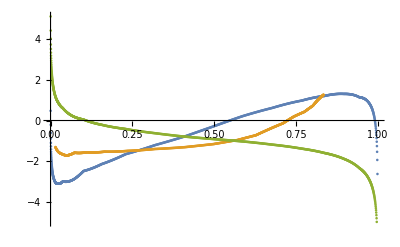

```mathematica
ListPlot[{linearizedReverseIsotherm4mA,linearizedReverseIsotherm2mA,linearizedReverseIsotherm1mA}]
```

```mathematica
frumkinFit4mA=Fit[linearizedReverseIsotherm4mA[[2;;(Length[linearizedReverseIsotherm4mA]-1)]],
{1,th},th]
```

-2.7475+4.26509 th

```mathematica
frumkinFit2mA=Fit[linearizedReverseIsotherm2mA[[2;;(Length[linearizedReverseIsotherm2mA]-1)]],
{1,th},th]
```

-2.02457+2.8767 th

```mathematica
frumkinFit1mA=Fit[linearizedReverseIsotherm1mA[[2;;(Length[linearizedReverseIsotherm1mA]-1)]],
{1,th},th]
```

0.854487-3.4664 th

```mathematica
frumkinIsotherm1mANSolve[c_]:=Quiet[NSolve[frumkinFit1mA==Log[c]-Log[th]+Log[1-th],th,Reals]][[1]]
```

```mathematica
frumkinIsotherm2mANSolve[c_]:=Quiet[NSolve[frumkinFit2mA==Log[c]-Log[th]+Log[1-th],th,Reals]][[1]]
```

```mathematica
frumkinIsotherm4mANSolve[c_]:=Quiet[NSolve[frumkinFit4mA==Log[c]-Log[th]+Log[1-th],th,Reals]][[1]]
```

```mathematica
fitDat1mA = Table[{dat1mA[[n,1]],N[th/.frumkinIsotherm1mANSolve[dat1mA[[n,2]]]]},{n,1,Length[dat1mA]}];
```

```mathematica
fitDat2mA = Table[{dat2mA[[n,1]],N[th/.frumkinIsotherm2mANSolve[dat2mA[[n,2]]]]},{n,1,Length[dat2mA]}];
```

```mathematica
fitDat4mA = Table[{dat4mA[[n,1]],N[th/.frumkinIsotherm4mANSolve[dat4mA[[n,2]]]]},{n,1,Length[dat4mA]}];
```

```mathematica
massPredictionDat1mA = Table[{dat1mA[[n,1]],
N[th/.frumkinIsotherm1mANSolve[dat1mA[[n,2]]]]
*(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]])+First[refReverseLogIsotherm4mA][[1]]},{n,1,Length[dat1mA]}];
```

```mathematica
massPredictionDat2mA = Table[{dat2mA[[n,1]],
N[th/.frumkinIsotherm2mANSolve[dat2mA[[n,2]]]]
*(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]])+First[refReverseLogIsotherm4mA][[1]]},{n,1,Length[dat2mA]}];
```

```mathematica
massPredictionDat4mA = Table[{dat4mA[[n,1]],
N[th/.frumkinIsotherm4mANSolve[dat4mA[[n,2]]]]
*(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]])+First[refReverseLogIsotherm4mA][[1]]},{n,1,Length[dat4mA]}];
```

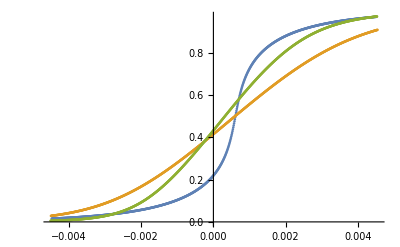

```mathematica
ListPlot[{fitDat1mA,fitDat2mA,fitDat4mA}]
```

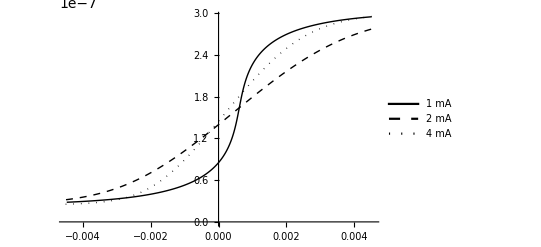

```mathematica
massPredictionDatPlot=ListLinePlot[{massPredictionDat1mA,massPredictionDat2mA,massPredictionDat4mA},PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[{"1 mA","2 mA","4 mA"},{0.75,0.25}]]
```

```mathematica
modifiedFrumkinFitInfo4mA=LinearModelFit[refReverseLogIsotherm4mANormCorrected[[2;;(Length[refReverseLogIsotherm4mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

FittedModel[-4.3502+7.40358 th+0.555019 (-Log[1-th]+Log[th])]

```mathematica
modifiedFrumkinFit4mA=Fit[refReverseLogIsotherm4mANormCorrected[[2;;(Length[refReverseLogIsotherm4mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

-4.3502+7.40358 th+0.555019 (-Log[1-th]+Log[th])

```mathematica
modifiedFrumkinFitInfo4mA=LinearModelFit[refReverseLogIsotherm4mANormCorrected[[2;;(Length[refReverseLogIsotherm4mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

FittedModel[-4.3502+7.40358 th+0.555019 (-Log[1-th]+Log[th])]

```mathematica
modifiedFrumkinFitInfo4mA["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
th | 1 | 13168.8 | 13168.8 | 79690.2 | 1.8837764078×10^-817
-Log[1-th]+Log[th] | 1 | 160.736 | 160.736 | 972.685 | 2.56323×10^-141
Error | 818 | 135.175 | 0.16525 |  | 
Total | 820 | 13464.7 |  |  |

```mathematica
modifiedFrumkinFitInfo4mA["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | -4.3502 | 0.0680447 | {-4.48377,-4.21664}
th | 7.40358 | 0.131765 | {7.14495,7.66222}
-Log[1-th]+Log[th] | 0.555019 | 0.017796 | {0.520088,0.58995}

```mathematica
a04mA=modifiedFrumkinFit4mA[[1]]
```

-4.3502

```mathematica
a14mA=modifiedFrumkinFit4mA[[2]][[1]]
```

7.40358

```mathematica
a24mA=modifiedFrumkinFit4mA[[3]][[1]]
```

0.555019

```mathematica
A4mA=-2*a24mA/a14mA
```

-0.149932

```mathematica
beta4mA=Exp[-a04mA/a24mA]
```

2534.98

```mathematica
gamma4mA=1/a24mA
```

1.80174

```mathematica
modifiedFrumkinFitInfo4mA["ParameterConfidenceIntervals"]
```

{{-4.48377,-4.21664},{7.14495,7.66222},{0.520088,0.58995}}

```mathematica
modifiedFrumkinFit2mA=Fit[refReverseLogIsotherm2mANormCorrected[[2;;(Length[refReverseLogIsotherm2mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

-3.42162+4.10408 th+0.419436 (-Log[1-th]+Log[th])

```mathematica
modifiedFrumkinFitInfo2mA=LinearModelFit[refReverseLogIsotherm2mANormCorrected[[2;;(Length[refReverseLogIsotherm2mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

FittedModel[-3.42162+4.10408 th+0.419436 (-Log[1-th]+Log[th])]

```mathematica
modifiedFrumkinFitInfo2mA["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | -3.42162 | 0.0372005 | {-3.49464,-3.3486}
th | 4.10408 | 0.0716434 | {3.96345,4.24471}
-Log[1-th]+Log[th] | 0.419436 | 0.0101799 | {0.399454,0.439418}

```mathematica
a02mA=modifiedFrumkinFit2mA[[1]]
```

-3.42162

```mathematica
a12mA=modifiedFrumkinFit2mA[[2]][[1]]
```

4.10408

```mathematica
a22mA=modifiedFrumkinFit2mA[[3]][[1]]
```

0.419436

```mathematica
A2mA=-2*a22mA/a12mA
```

-0.204399

```mathematica
beta2mA=Exp[-a02mA/a22mA]
```

3490.07

```mathematica
gamma2mA=1/a22mA
```

2.38416

```mathematica
modifiedFrumkinFit1mA=Fit[refReverseLogIsotherm1mANormCorrected[[2;;(Length[refReverseLogIsotherm1mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

-2.34523+1.77185 th+0.252778 (-Log[1-th]+Log[th])

```mathematica
modifiedFrumkinFitInfo1mA=LinearModelFit[refReverseLogIsotherm1mANormCorrected[[2;;(Length[refReverseLogIsotherm1mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

FittedModel[-2.34523+1.77185 th+0.252778 (-Log[1-th]+Log[th])]

```mathematica
modifiedFrumkinFitInfo1mA["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | -2.34523 | 0.0275495 | {-2.3993,-2.29115}
th | 1.77185 | 0.053076 | {1.66766,1.87603}
-Log[1-th]+Log[th] | 0.252778 | 0.00734617 | {0.238358,0.267198}

```mathematica
a01mA=modifiedFrumkinFit1mA[[1]]
```

-2.34523

```mathematica
a11mA=modifiedFrumkinFit1mA[[2]][[1]]
```

1.77185

```mathematica
a21mA=modifiedFrumkinFit1mA[[3]][[1]]
```

0.252778

```mathematica
A1mA=-2*a21mA/a11mA
```

-0.285328

```mathematica
beta1mA=Exp[-a01mA/a21mA]
```

10697.9

```mathematica
gamma4mA=1/a21mA
```

3.95604

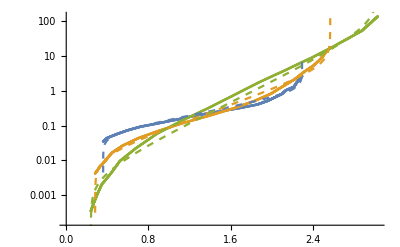

```mathematica
Show[refReverseIsothermLogPlot,Plot[{modifiedFrumkinFit1mA/.th->((m-First[refReverseLogIsotherm1mA][[1]])/(Last[refReverseLogIsotherm1mA][[1]]-First[refReverseLogIsotherm1mA][[1]])),
modifiedFrumkinFit2mA/.th->((m-First[refReverseLogIsotherm2mA][[1]])/(Last[refReverseLogIsotherm2mA][[1]]-First[refReverseLogIsotherm2mA][[1]])),
modifiedFrumkinFit4mA/.th->((m-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]]))},
{m,0,Last[refReverseLogIsotherm4mA][[1]]},PlotStyle->Dashed]]
```

```mathematica
modifiedFrumkinFit4mAAbsolute=Fit[refReverseLogIsotherm4mANormCorrectedAbsolute[[2;;(Length[refReverseLogIsotherm4mANormCorrectedAbsolute]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

Part::take: Cannot take positions 2 through -1 in refReverseLogIsotherm4mANormCorrectedAbsolute.

Fit::fitd: First argument refReverseLogIsotherm4mANormCorrectedAbsolute⟦2;;-1⟧ in Fit is not a list or a rectangular array.

Part::take: Cannot take positions 2 through -1 in refReverseLogIsotherm4mANormCorrectedAbsolute.

Fit::fitd: First argument refReverseLogIsotherm4mANormCorrectedAbsolute⟦2;;-1⟧ in Fit is not a list or a rectangular array.

Fit[refReverseLogIsotherm4mANormCorrectedAbsolute⟦2;;-1⟧,{1,th,-Log[1-th]+Log[th]},th]

```mathematica
modifiedFrumkinFit2mAAbsolute=Fit[refReverseLogIsotherm2mANormCorrectedAbsolute,{1,
th,
Log[th]-Log[1-th]},th]
```

Fit::fitd: First argument refReverseLogIsotherm2mANormCorrectedAbsolute in Fit is not a list or a rectangular array.

Fit[refReverseLogIsotherm2mANormCorrectedAbsolute,{1,th,-Log[1-th]+Log[th]},th]

```mathematica
modifiedFrumkinFit1mAAbsolute=Fit[refReverseLogIsotherm1mANormCorrectedAbsolute,{1,
th,
Log[th]-Log[1-th]},th]
```

Fit::fitd: First argument refReverseLogIsotherm1mANormCorrectedAbsolute in Fit is not a list or a rectangular array.

Fit[refReverseLogIsotherm1mANormCorrectedAbsolute,{1,th,-Log[1-th]+Log[th]},th]

```mathematica
Show[refReverseIsothermLogPlot,Plot[{modifiedFrumkinFit1mAAbsolute/.th->((m-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]])),
modifiedFrumkinFit2mAAbsolute/.th->((m-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]])),
modifiedFrumkinFit4mAAbsolute/.th->((m-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]]))},
{m,0,Last[refReverseLogIsotherm4mA][[1]]},PlotStyle->Dashed]]
```

General::ivar: -0.08564 is not a valid variable.

General::ivar: -0.0634836 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
modifiedFrunkinIsotherm1mA[c_]:=FindRoot[modifiedFrumkinFit1mA==Log[c],{th,0.5}]
```

```mathematica
modifiedFrunkinIsotherm2mA[c_]:=FindRoot[modifiedFrumkinFit2mA==Log[c],{th,0.5}]
```

```mathematica
modifiedFrunkinIsotherm4mA[c_]:=FindRoot[modifiedFrumkinFit4mA==Log[c],{th,0.5}]
```

```mathematica
modifiedFrunkinIsotherm1mANSolve[c_]:=Quiet[NSolve[modifiedFrumkinFit1mA==Log[c],th,Reals]][[1]]
```

```mathematica
modifiedFrunkinIsotherm2mANSolve[c_]:=Quiet[NSolve[modifiedFrumkinFit2mA==Log[c],th,Reals]][[1]]
```

```mathematica
modifiedFrunkinIsotherm4mANSolve[c_]:=Quiet[NSolve[modifiedFrumkinFit4mA==Log[c],th,Reals]][[1]]
```

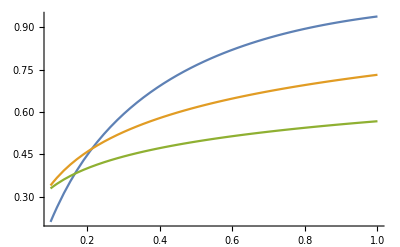

```mathematica
Plot[{th/.modifiedFrunkinIsotherm1mA[c],th/.modifiedFrunkinIsotherm2mA[c],th/.modifiedFrunkinIsotherm4mA[c]},{c,0.1,1}]
```

```mathematica
fit1mA = Table[{dat1mA[[n,1]],N[th/.modifiedFrunkinIsotherm1mANSolve[dat1mA[[n,2]]]]},{n,1,Length[dat1mA]}];
```

```mathematica
fit2mA = Table[{dat2mA[[n,1]],N[th/.modifiedFrunkinIsotherm2mANSolve[dat2mA[[n,2]]]]},{n,1,Length[dat2mA]}];
```

```mathematica
fit4mA = Table[{dat4mA[[n,1]],N[th/.modifiedFrunkinIsotherm4mANSolve[dat4mA[[n,2]]]]},{n,1,Length[dat4mA]}];
```

```mathematica
massPrediction1mA = Table[{dat1mA[[n,1]],
N[th/.modifiedFrunkinIsotherm1mANSolve[dat1mA[[n,2]]]]
*(Last[refReverseLogIsotherm1mA][[1]]-First[refReverseLogIsotherm1mA][[1]])+First[refReverseLogIsotherm1mA][[1]]},{n,1,Length[dat1mA]}];
```

```mathematica
massPrediction2mA = Table[{dat2mA[[n,1]],
N[th/.modifiedFrunkinIsotherm2mANSolve[dat2mA[[n,2]]]]
*(Last[refReverseLogIsotherm2mA][[1]]-First[refReverseLogIsotherm2mA][[1]])+First[refReverseLogIsotherm2mA][[1]]},{n,1,Length[dat2mA]}];
```

```mathematica
massPrediction4mA = Table[{dat4mA[[n,1]],
N[th/.modifiedFrunkinIsotherm4mANSolve[dat4mA[[n,2]]]]
*(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]])+First[refReverseLogIsotherm4mA][[1]]},{n,1,Length[dat4mA]}];
```

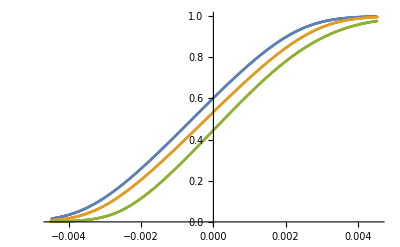

```mathematica
ListPlot[{fit1mA,fit2mA,fit4mA}]
```

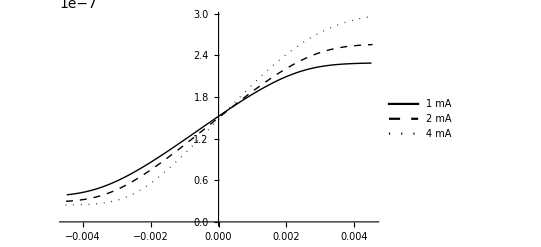

```mathematica
massPredictionPlot=ListLinePlot[{massPrediction1mA,massPrediction2mA,massPrediction4mA},PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[{"1 mA","2 mA","4 mA"},{0.75,0.25}]]
```

```mathematica
Show
```

Show

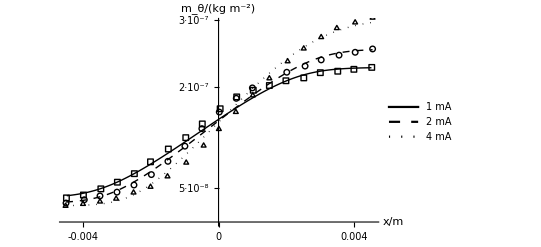

```mathematica
Show[massPredictionPlot,trueMassPlot,AxesLabel->{Text[x]/Text[m],Subscript[Text[m],Text[θ]]/Text[kg m^"-2"]},
LabelStyle->Directive[Black],
Ticks->{{-0.004,0,0.004},
{{5.0*^-8,Text[5]·Text[10]^Text[-8]},
{1.0*^-7, ""},{1.5*^-7, ""},
{2.0*^-7,Text[2]·Text[10]^Text[-7]},
{2.5*^-7,""},
{3.0*^-7,Text[3]·Text[10]^Text[-7]}}}]
```

```mathematica
lineStyles={Directive[Black,Thick],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]}
```

{Directive[GrayLevel[0],Thickness[Large]],Directive[GrayLevel[0],Thickness[Large],Dashing[{Small,Small}]],Directive[GrayLevel[0],Thickness[Large],Dashing[{0,Small}]]}

```mathematica
lineStyles={Directive[Black,Thick],Directive[Black,Thick],Directive[Black,Thick]}
```

{Directive[GrayLevel[0],Thickness[Large]],Directive[GrayLevel[0],Thickness[Large]],Directive[GrayLevel[0],Thickness[Large]]}

```mathematica
{fm1,fm2,fm3}=Graphics/@{{EdgeForm[Thick],White,Polygon[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}]},{EdgeForm[Thick],White,Disk[{0,0},1]},{EdgeForm[Thick],White,Polygon[{{-0.5,-0.5},{0.5,-0.5},{0,(Sqrt[3]-1)/2},{-0.5,-0.5}}]}}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
rasteredMarkers={Rasterize[fm1,RasterSize->15,ImageSize->15,Background->None],Rasterize[fm2,RasterSize->15,ImageSize->15],Rasterize[fm3,RasterSize->15,ImageSize->15]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
plegend2=PointLegend[Table[Black,{3}],{"","",""},LegendMarkerSize->{50,10},LegendMarkers->{{m1,1},{m2,1},{m3,1}},LabelStyle->{GrayLevel[0.0],12}]
```

```mathematica
llegend=LineLegend[lineStyles,{"1 mA","2 mA","4 mA"},LegendMarkerSize->{50,10},LabelStyle->{GrayLevel[0.0],12}]
```

```mathematica
pllegend=LineLegend[lineStyles,{"1 mA","2 mA","4 mA"},LegendMarkerSize->{50,15},LegendMarkers->rasteredMarkers,LabelStyle->{GrayLevel[0.0],12}]
```

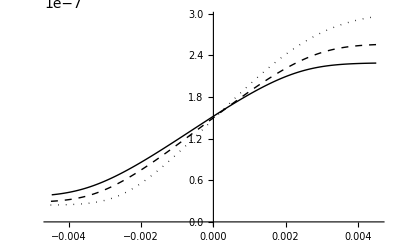

```mathematica
massPredictionPlotFullLegend=ListLinePlot[{massPrediction1mA,massPrediction2mA,massPrediction4mA},PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[pllegend,{0.75,0.25}]]
```

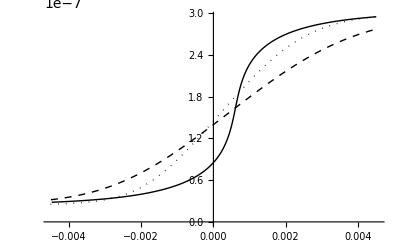

```mathematica
massPredictionDatPlotFullLegend=ListLinePlot[{massPredictionDat1mA,massPredictionDat2mA,massPredictionDat4mA},PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[pllegend,{0.75,0.25}]]
```

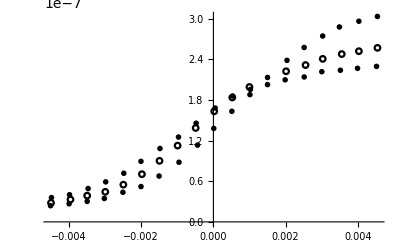

```mathematica
trueMassPlotMarkers=ListPlot[{adMass1mA,adMass2mA,adMass4mA},PlotStyle->Black,PlotMarkers->Table[{s,0.03},{s,{m1,m2,m3}}]]
```

```mathematica
trueMassPlotWithRawLegend=ListPlot[{adMass1mA,adMass2mA,adMass4mA},PlotStyle->Black,PlotMarkers->Table[{s,0.03},{s,{m1,m2,m3}}],PlotLegends->Placed[plegend2,{0.75,0.25}]]
```

-Graphics-

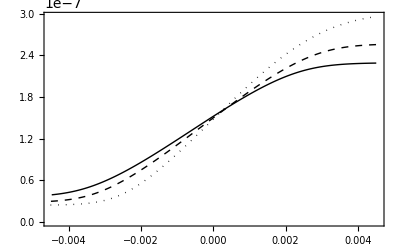

```mathematica
massPredictionPlotFramed=ListLinePlot[{massPrediction1mA,massPrediction2mA,massPrediction4mA},PlotStyle->{Directive[Black,Thick,Automatic],Directive[Black,Thick,Dashed],Directive[Black,Thick,Dotted]},PlotLegends->Placed[pllegend,{0.75,0.25}],Frame->True,Axes->False]
```

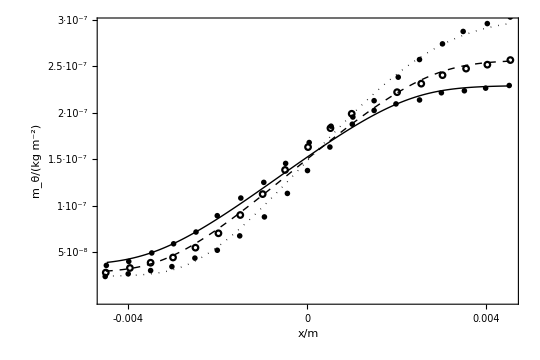

```mathematica
Show[massPredictionPlotFullLegend,trueMassPlotMarkers,FrameLabel->{Text[x]/Text[m],Subscript[Text[m],Text[θ]]/Text[kg m^"-2"]},
LabelStyle->Directive[Black],
FrameTicks->{{{
{5.0*^-8,Text[5]·Text[10]^Text[-8]},
{1.0*^-7, Text[1]·Text[10]^Text[-7]},
{1.5*^-7, Text[1.5]·Text[10]^Text[-7]},
{2.0*^-7,Text[2]·Text[10]^Text[-7]},
{2.5*^-7,Text[2.5]·Text[10]^Text[-7]},
{3.0*^-7,Text[3]·Text[10]^Text[-7]}},None},{{-0.004,0,0.004},None}},Frame->True,Axes->False,AspectRatio->1/1.5]
```

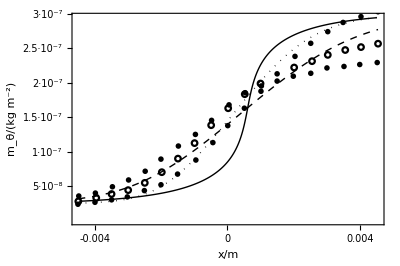

```mathematica
Show[massPredictionDatPlotFullLegend,trueMassPlotMarkers,FrameLabel->{Text[x]/Text[m],Subscript[Text[m],Text[θ]]/Text[kg m^"-2"]},
LabelStyle->Directive[Black],
FrameTicks->{{{
{5.0*^-8,Text[5]·Text[10]^Text[-8]},
{1.0*^-7, Text[1]·Text[10]^Text[-7]},
{1.5*^-7, Text[1.5]·Text[10]^Text[-7]},
{2.0*^-7,Text[2]·Text[10]^Text[-7]},
{2.5*^-7,Text[2.5]·Text[10]^Text[-7]},
{3.0*^-7,Text[3]·Text[10]^Text[-7]}},None},{{-0.004,0,0.004},None}},Frame->True,Axes->False,AspectRatio->1/1.5]
```